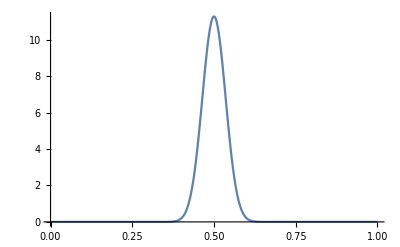

```mathematica
Plot[PDF[BetaDistribution[100,100],x],{x,0,1},PlotRange->All]
```

```mathematica
OneDimentionMoyalBracket[A_,H_,x_,p_,end_]:=Sum[(-1)^j/((2j+1)!)*(h/4Pi)^(2j)*
Sum[Binomial[2j+1,k]*(-1)^(2j+1-k)*
Nest[D[#,p]&,Nest[D[#,x]&,A,k],2j+1-k]*Nest[D[#,x]&,Nest[D[#,p]&,H,k],2j+1-k]
,{k,0,2j+1}],{j,0,end}];
```

```mathematica
Bracket[A_,H_,xList_,pList_,end_]:=Sum[(-1)^j/((2j+1)!)*(h/4Pi)^(2j)*
Sum[Binomial[2j+1,k]*(-1)^(2j+1-k)*
Nest[D[#,p]&,Nest[D[#,x]&,A,k],2j+1-k]*Nest[D[#,x]&,Nest[D[#,p]&,H,k],2j+1-k]
,{k,0,2j+1}],{j,0,end}]
```

```mathematica
MoyalBracket[f[x],p^2/(2m)+V[x],x,p,1]//Simplify
```

(p f'[x])/m

```mathematica
Binomial[2j+1,1]
```

1+2 j

```mathematica
MoyalBracket[p,p^2/(2m)+V[x],x,p,10]//Simplify
```

-V'[x]

```mathematica
MoyalBracket[-p/m*V'[x],p^2/(2m)+V[x],x,p,10]
```

V'[x]^2/m-(p^2 V''[x])/m^2

```mathematica
MoyalBracket[x^10,p^2/(2m)+V[p],{{x,p}},10]
```

10 x^9 (p/m+V'[p])-15/2 h^2 π^2 x^7 V^(3)[p]+63/64 h^4 π^4 x^5 V^(5)[p]-15/512 h^6 π^6 x^3 V^(7)[p]+(5 h^8 π^8 x V^(9)[p])/32768

```mathematica
NestList[MoyalBracket[#,p^2/(2m)+V[x],x,p,10]&,x,7]
```

{x,p/m,-V'[x]/m,-(p V''[x])/m^2,(V'[x] V''[x])/m^2-(p^2 V^(3)[x])/m^3,(2 p V'[x] V^(3)[x])/m^3+(p (V''[x]^2/m^2+(V'[x] V^(3)[x])/m^2-(p^2 V^(4)[x])/m^3))/m,-(h^2 π^2 V^(3)[x] V^(4)[x])/(16 m^4)-V'[x] ((2 V'[x] V^(3)[x])/m^3-(2 p^2 V^(4)[x])/m^4+(V''[x]^2/m^2+(V'[x] V^(3)[x])/m^2-(p^2 V^(4)[x])/m^3)/m)+(p ((2 p V''[x] V^(3)[x])/m^3+(2 p V'[x] V^(4)[x])/m^3+(p ((3 V''[x] V^(3)[x])/m^2+(V'[x] V^(4)[x])/m^2-(p^2 V^(5)[x])/m^3))/m))/m,-(h^2 p π^2 V^(3)[x] V^(5)[x])/(4 m^5)-V'[x] ((6 p V'[x] V^(4)[x])/m^4+(p ((2 V''[x] V^(3)[x])/m^3+(2 V'[x] V^(4)[x])/m^3-(2 p^2 V^(5)[x])/m^4+((3 V''[x] V^(3)[x])/m^2+(V'[x] V^(4)[x])/m^2-(p^2 V^(5)[x])/m^3)/m))/m+((2 p V''[x] V^(3)[x])/m^3+(2 p V'[x] V^(4)[x])/m^3+(p ((3 V''[x] V^(3)[x])/m^2+(V'[x] V^(4)[x])/m^2-(p^2 V^(5)[x])/m^3))/m)/m)+1/m p (-(h^2 π^2 (V^(4)[x])^2)/(16 m^4)-V''[x] ((2 V'[x] V^(3)[x])/m^3-(2 p^2 V^(4)[x])/m^4+(V''[x]^2/m^2+(V'[x] V^(3)[x])/m^2-(p^2 V^(4)[x])/m^3)/m)-(h^2 π^2 V^(3)[x] V^(5)[x])/(16 m^4)-V'[x] ((2 V''[x] V^(3)[x])/m^3+(2 V'[x] V^(4)[x])/m^3-(2 p^2 V^(5)[x])/m^4+((3 V''[x] V^(3)[x])/m^2+(V'[x] V^(4)[x])/m^2-(p^2 V^(5)[x])/m^3)/m)+(p ((2 p (V^(3)[x])^2)/m^3+(4 p V''[x] V^(4)[x])/m^3+(2 p V'[x] V^(5)[x])/m^3+(p ((3 (V^(3)[x])^2)/m^2+(4 V''[x] V^(4)[x])/m^2+(V'[x] V^(5)[x])/m^2-(p^2 V^(6)[x])/m^3))/m))/m)}

```mathematica
NestList[MoyalBracket[#,p^2/(2m)-1/x,x,p,10]&,x,7]
```

{x,p/m,-1/(m x^2),(2 p)/(m^2 x^3),-2/(m^2 x^5)-(6 p^2)/(m^3 x^4),(p (10/(m^2 x^6)+(24 p^2)/(m^3 x^5)))/m+(12 p)/(m^3 x^6),(p ((p (-60/(m^2 x^7)-(120 p^2)/(m^3 x^6)))/m-(72 p)/(m^3 x^7)))/m+(9 h^2 π^2)/(m^4 x^9)-((10/(m^2 x^6)+(24 p^2)/(m^3 x^5))/m+12/(m^3 x^6)+(48 p^2)/(m^4 x^5))/x^2,(p ((p ((p (420/(m^2 x^8)+(720 p^2)/(m^3 x^7)))/m+(504 p)/(m^3 x^8)))/m-(81 h^2 π^2)/(m^4 x^10)+(2 ((10/(m^2 x^6)+(24 p^2)/(m^3 x^5))/m+12/(m^3 x^6)+(48 p^2)/(m^4 x^5)))/x^3-((-60/(m^2 x^7)-(120 p^2)/(m^3 x^6))/m-72/(m^3 x^7)-(240 p^2)/(m^4 x^6))/x^2))/m-(180 h^2 p π^2)/(m^5 x^10)-(((p (-60/(m^2 x^7)-(120 p^2)/(m^3 x^6)))/m-(72 p)/(m^3 x^7))/m+(p ((-60/(m^2 x^7)-(120 p^2)/(m^3 x^6))/m-72/(m^3 x^7)-(240 p^2)/(m^4 x^6)))/m-(144 p)/(m^4 x^7))/x^2}

```mathematica
DerivativeExpand[function1_,function2_,variablelist_,power_]:=Module[{A,B,a,b,x,Regularizer,Coefficientlist,listtemp},
Regularizer[SubList_]:=Module[{temp},
temp=If[Nor[MatchQ[#,_Integer],MatchQ[#,_List]],{#,1},#]&/@SubList;
If[MatchQ[First[temp],_Integer],,PrependTo[temp,1]];
temp
];
listtemp=Regularizer/@ReleaseHold[Hold[Evaluate@Expand[Total[A[#1]*B[#2]-A[#2]B[#1]&@@@variablelist]^power]]/.{Power->List,Times->List,Plus->List}]/.{A[x_]->{a,x},B[x_]->{b,x}};
Coefficientlist=First/@listtemp;
listtemp=Map[Drop[#,1]&,Map[GatherBy[#,First]&,Map[Flatten,Drop[#,1]&/@listtemp,{2}]],{3}];
(*Now the first element in each list refers to the derivatives of the first function*)
Coefficientlist.(Fold[D,function1,#[[1]]]*Fold[D,function2,#[[2]]]&/@listtemp)
];
MoyalBracket[A_,H_,variableList_,end_]:=Sum[(-1)^j/((2j+1)!)*(h/4Pi)^(2j)*DerivativeExpand[A,H,variableList,2j+1],{j,0,end}];
```

```mathematica
MoyalBracket[A[x,p],H[x,p],{{x,p}},3]
```

H^(0,1)[x,p] A^(1,0)[x,p]-A^(0,1)[x,p] H^(1,0)[x,p]-1/96 h^2 π^2 (-3 H^(1,2)[x,p] A^(2,1)[x,p]+3 A^(1,2)[x,p] H^(2,1)[x,p]+H^(0,3)[x,p] A^(3,0)[x,p]-A^(0,3)[x,p] H^(3,0)[x,p])+1/30720 h^4 π^4 (10 H^(2,3)[x,p] A^(3,2)[x,p]-10 A^(2,3)[x,p] H^(3,2)[x,p]-5 H^(1,4)[x,p] A^(4,1)[x,p]+5 A^(1,4)[x,p] H^(4,1)[x,p]+H^(0,5)[x,p] A^(5,0)[x,p]-A^(0,5)[x,p] H^(5,0)[x,p])-1/20643840 h^6 π^6 (-35 H^(3,4)[x,p] A^(4,3)[x,p]+35 A^(3,4)[x,p] H^(4,3)[x,p]+21 H^(2,5)[x,p] A^(5,2)[x,p]-21 A^(2,5)[x,p] H^(5,2)[x,p]-7 H^(1,6)[x,p] A^(6,1)[x,p]+7 A^(1,6)[x,p] H^(6,1)[x,p]+H^(0,7)[x,p] A^(7,0)[x,p]-A^(0,7)[x,p] H^(7,0)[x,p])

```mathematica
DerivativeExpand[a[x1,p1],b[x1,p1],{{x1,p1}},3]
```

-3 b^(1,2)[x1,p1] a^(2,1)[x1,p1]+3 a^(1,2)[x1,p1] b^(2,1)[x1,p1]+b^(0,3)[x1,p1] a^(3,0)[x1,p1]-a^(0,3)[x1,p1] b^(3,0)[x1,p1]

```mathematica
MoyalBracket[p1^2*x1^3,(p1^4+p2^2+p3^2)/(2 m)+V[x1,x2,x3],{{x1,p1},{x2,p2},{x3,p3}},10]
```

-(3 h^2 p1^3 π^2)/(4 m)+(6 p1^5 x1^2)/m-2 p1 x1^3 V^(1,0,0)[x1,x2,x3]

```mathematica
MoyalBracket[f[x1,x2]*g[p1,p2],(p1^2+p2^2)/(2m)+x1^2+x2^2,{{x1,p1},{x2,p2}},10]
```

(p2 g[p1,p2] f^(0,1)[x1,x2])/m-2 x2 f[x1,x2] g^(0,1)[p1,p2]+(p1 g[p1,p2] f^(1,0)[x1,x2])/m-2 x1 f[x1,x2] g^(1,0)[p1,p2]